```mathematica
Needs["Quantum`Computing`"];
```

## ZZZ

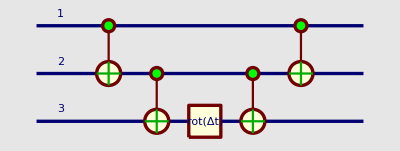

{ⅇ^(-ⅈ Δt) a[1],ⅇ^(ⅈ Δt) a[2],ⅇ^(ⅈ Δt) a[3],ⅇ^(-ⅈ Δt) a[4],ⅇ^(ⅈ Δt) a[5],ⅇ^(-ⅈ Δt) a[6],ⅇ^(-ⅈ Δt) a[7],ⅇ^(ⅈ Δt) a[8]}

{ⅇ^(-ⅈ Δt) a[1],ⅇ^(ⅈ Δt) a[2],ⅇ^(ⅈ Δt) a[3],ⅇ^(-ⅈ Δt) a[4],ⅇ^(ⅈ Δt) a[5],ⅇ^(-ⅈ Δt) a[6],ⅇ^(-ⅈ Δt) a[7],ⅇ^(ⅈ Δt) a[8]}

{1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,Z]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{1,0}],1];
psi=Array[a,2^3];
U1.psi
U2.psi
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

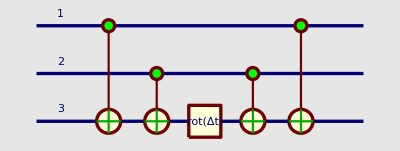

{ⅇ^(-ⅈ Δt) a[1],ⅇ^(ⅈ Δt) a[2],ⅇ^(ⅈ Δt) a[3],ⅇ^(-ⅈ Δt) a[4],ⅇ^(ⅈ Δt) a[5],ⅇ^(-ⅈ Δt) a[6],ⅇ^(-ⅈ Δt) a[7],ⅇ^(ⅈ Δt) a[8]}

{ⅇ^(-ⅈ Δt) a[1],ⅇ^(ⅈ Δt) a[2],ⅇ^(ⅈ Δt) a[3],ⅇ^(-ⅈ Δt) a[4],ⅇ^(ⅈ Δt) a[5],ⅇ^(-ⅈ Δt) a[6],ⅇ^(-ⅈ Δt) a[7],ⅇ^(ⅈ Δt) a[8]}

{1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,Z]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{1,0}],1];
psi=Array[a,2^3];
U1.psi
U2.psi
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```